# Relativistic and Nonrelativistic Dynamics of a Charged Particle in Electromagnetic Waves

## Jack McArthur, MATH 528L

## Introduction

### Electromagnetism

The electromagnetic force on point particle with charge q at point r is given by Lorentz’s equation  
F  =  dp/dt = q (E +  v × B) , 
which involves the following 3-dimensional vector quantities :
	E( r , t ), the electric field at point r at time t,
	B( r , t ),  the magnetic field at point r at time t,
	v, the particle’s velocity dr/dt,
	p, the particle’s momentum, or its velocity v multiplied by the its mass m.
This equation is a second order ordinary differential equation in t, owing to the dp/dt term. The equations of motion of a charged particle particle in various electromagnetic fields can be determined by substituting different forms for E and B into the Lorentz equation.

### Nonrelativistic vs. Relativistic Dynamics

In the above equation, if q (E +  v × B) = dp/dt ,  the momentum of a particle can become arbitrarily large in the right electric and magnetic field. If we substitute mv for p, we get the equation F  =  m dv/dt  , better known as F = ma . Therefore, if q (E +  v × B) = ma, a particle in the right electric and magnetic field can be accelerated infinitely, and possess any speed, 0 < |v| < ∞. This is not physically possible due to the cosmic speed limit c, the speed of light in a vacuum. This presents a contradiction, as p can be arbitrarily large despite being proportional to v, which cannot be. As a solution, we redefine p to be equal to mγ v , where γ is the Lorenz factor 1/(√(1-v^2/c^2)). The approximation p = mv is therefore true at low velocities, where γ ≈ 1, but as |v| approaches c, p goes to ∞.

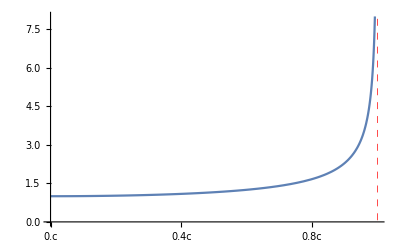
-Graphics-γ as a function of v

```mathematica
Labeled[
Plot[1/Sqrt[1-v^2],{v,0,1},PlotRange->{0,8},GridLinesStyle->Directive[Red,Thick,Dashed],GridLines->{{1},{}},
Ticks->{Table[{0.2 v,ToString[0.2 v]<>"c"},{v,0,5}],Automatic}],
"γ as a function of v",Top]
```

In physics, it is common to model particle motion within the nonrelativistic approximation, in which γ = 1, though this is not rigorously accurate and fails for velocities that are considerable fractions of the speed of light. In this notebook, relativistic vs. nonrelativistic models for particle motion in various EM fields are compared, and interesting notes about the dynamics in each scenario are mentioned.

## Results

### Homogeneous (Crossed) Fields

A simple case of an electromagnetic field in three dimensions is the homogenous crossed field E = E_0 (1 , 0 , 0) and B = B_0 (0 , 1 , 0). This field has no time dependence, and the corresponding system of ODEs for the nonrelativistic case is given below:

```mathematica
homogeneousfieldmotion=Module[
{c=1,E,B,
r={x[t],y[t],z[t]},
v={x'[t],y'[t],z'[t]}},
p=m0 v;
E= {E0,0,0};
B= {0,B0,0};
First@Solve[D[p,t]==q(E+Cross[v,B]),
{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify]
```

{x''[t]==(q (E0-B0 z'[t]))/m0,y''[t]==0,(B0 q x'[t])/m0==z''[t]}

This system of ODEs has an exact solution.

```mathematica
DSolveValue[Join[homogeneousfieldmotion,{x[0]==0,y[0]==0,z[0]==0,
x'[0]==Subscript[v, x0],y'[0]==Subscript[v, y0],z'[0]==Subscript[v, z0]}],{x[t],y[t],z[t]},t]/.{E0->ℰ,B0->ℬ}//FullSimplify
```

{(m0 (ℬ Sin[(q t ℬ)/m0] v_x0-(-1+Cos[(q t ℬ)/m0]) (ℰ-ℬ v_z0)))/(q ℬ^2),t v_y0,(q t ℬ ℰ-m0 ℬ (-1+Cos[(q t ℬ)/m0]) v_x0+m0 Sin[(q t ℬ)/m0] (-ℰ+ℬ v_z0))/(q ℬ^2)}

The solutions as the strengths of the E and B fields and the particle’s charge to mass ratio varied can be manipulated below.

```mathematica
Manipulate[
Tmax=15;
mvmth=
DSolveValue[Join[homogeneousfieldmotion,{x[0]==0,y[0]==0,z[0]==0,
x'[0]==0,y'[0]==v0y,z'[0]==v0z}],{x[t],y[t],z[t]},t]/.
{E0->E0v,B0->B0v,m0 ->1,q->qv,v0y->pt[[1]],v0z->pt[[2]]};

Grid[{
{"Homogeneous field motion"},
{Show[
ParametricPlot3D[{{0,pt[[1]] t/10,pt[[2]] t/10},mvmth},{t,0,Tmax},
PlotRange->{{-0.4,0.8},{0,2.},{-0.2,2.}},PlotPoints->40*Tmax,
ImageSize->{300,300},PlotStyle->{Hue[0.33,0.93,0.57],Orange},
AxesLabel->{x,y,z},BoxRatios->Automatic],
Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,B0v,0}},0.01]]}],
Graphics3D[{Blue,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{2 E0v,0,0}},0.01]]}]]}
}],

{{E0v,0.15,Style["electric field strength",Blue]},0.0,0.6,0.05,Appearance->"Labeled"},
{{B0v,1.4,Style["magnetic field strength",Red]},0.0,2.,0.05,Appearance->"Labeled"},
{{qv,2,"charge/mass ratio"},0.0,20.,0.5,Appearance->"Labeled"},
{{pt,{0.12,0.47},Style["initial y/z velocity",Hue[0.33,0.93,0.57]]},{0,0},{0.7,0.7},ImageSize->Tiny,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

### Nonrelativistic and Relativistic Dynamics in Transverse Waves

We now look at the dynamics of a particle subjected to a transverse electromagnetic wave. Transverse waves are moving waves that propagate in a direction and oscillate perpendicular to the direction of propagation. A transverse electromagnetic wave consists of oscillating E and B fields that oscillate perpendicularly to each other and propagates at the speed of light, and the magnitudes of the E and B fields are time dependent but not spatially dependent.

```mathematica
Import["C:\Users\jackm\OneDrive\Documents\UNC Math 528L\Electromagneticwave3Dgif.gif","Animation",ControlPlacement->Top,AnimationRunning->False]
```

https://commons.wikimedia.org/wiki/File:Electromagneticwave3D.gif

Nonrelativistic equations of motion of a charged particle in a plane wave propagating in the ẑ direction:

```mathematica
nonrelplanewavemotion=Module[
{c=1,E,B,
r={x[t],y[t],z[t]},
γ=(1-(x'[t]^2+y'[t]^2+z'[t]^2)/c^2)^(-1/2),
v={x'[t],y'[t],z'[t]},
k={0,0,1}},
p=m0 v;
E= {E0 Sin[k.r-c t],0,0};
B= {0,B0 Sin[k.r-c t],0};
First@Solve[D[p,t]==q(E+Cross[v,B]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[nonrelplanewavemotion]
```

x''[t]==(q Sin[t-z[t]] (-E0+B0 z'[t]))/m0
y''[t]==0
(B0 q Sin[t-z[t]] x'[t])/m0+z''[t]==0

Relativistic motion of a particle in a plane wave; the momentum p in the Lorentz force is corrected by a factor of 1/γ :

```mathematica
planewavemotion=Module[
{c=1,E,B,
r={x[t],y[t],z[t]},
γ=(1-(x'[t]^2+y'[t]^2+z'[t]^2)/c^2)^(-1/2),
v={x'[t],y'[t],z'[t]},
k={0,0,1}},
γ=(1-v.v/c^2)^(-1/2);
p=γ m0 v;
E= {E0 Sin[k.r-c t],0,0};
B= {0,B0 Sin[k.r-c t],0};
First@Solve[D[p,t]==q(E+Cross[v,B]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[planewavemotion]
```

x''[t]==(q Sin[t-z[t]] (-E0+E0 x'[t]^2+B0 z'[t]) √(1-x'[t]^2-y'[t]^2-z'[t]^2))/m0
y''[t]==(E0 q Sin[t-z[t]] x'[t] y'[t] √(1-x'[t]^2-y'[t]^2-z'[t]^2))/m0
z''[t]==(q Sin[t-z[t]] x'[t] (-B0+E0 z'[t]) √(1-x'[t]^2-y'[t]^2-z'[t]^2))/m0

Manipulable parametric plots of the nonrelativistic and relativistic trajectories of a charged particle in a plane wave.

```mathematica
Manipulate[
Tmax=30;
mvmtnr=
NDSolveValue[Join[nonrelplanewavemotion/.{m0->1.,q->qv,E0->E0v,B0->(B0v*E0v)},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];
mvmtr=
NDSolveValue[Join[planewavemotion/.{m0->1.,q->qv,E0->E0v,B0->(B0v*E0v)},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

Grid[{{"Nonrelativistic","Relativistic"},
{ParametricPlot[{mvmtnr[[1]][t],mvmtnr[[3]][t]},{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}],
ParametricPlot[{mvmtr[[1]][t],mvmtr[[3]][t]},{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}]}}],

{{E0v,0.13,"electric field strength"},0.,8.,0.01,Appearance->"Labeled"},
{{B0v,43.,"magnetic/electric field strength ratio"},0.05,99.,0.05,Appearance->"Labeled"},
{{v0z,0.12,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{qv,1.42,"charge/mass ratio of particle"},-2,2,0.02,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

The solutions above are the sum of a linear drifting component and a more complex periodic component. If we could separate out only the solution’s periodic component, also known as the motion in the drift coordinates, we could learn more about the behaviors of the nonrelativistic and relativistic systems as the parameters are varied.

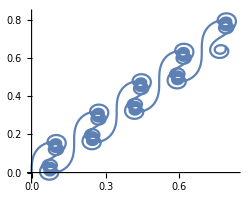
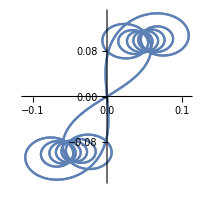
-Graphics- → -Graphics-

```mathematica
(*this algorithm finds the necessary linear transformation to eliminate the drift from the above trajectory*)(*finds the repeating unit of a list with an arithmatic pattern*)
patternfind[list_]:=
Module[{table,rootpd},
table=Table[-list[[2n+2]]+2 list[[n+2]]-list[[2]],{n,0,Floor[Length[list]/2]-1}];(*diff. of list[[x]] and list[[P+x]] vs. list[[P+x]] and list[[2P+x]]; tries every possible P*)
rootpd=First@First@Position[Abs[table],Min[Abs[Delete[table,1]]]]-1 (*chooses minimum difference; this is how many roots are in one period*)
]

Tmax=30;
(*the algorithm uses the arithmatic patterns in the roots of x'[t] to find the drift (Δx,Δz) in time Δt*)
(*reap/sow pulls out all points where x'[t] = 0 as it solves the system of ODEs*)
{xmvmt,xroots}=Reap@NDSolveValue[Join[planewavemotion/.{m0->1.,q->4.2,E0->0.11,B0->5.3},{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==0.4,
WhenEvent[x'[t]==0,Sow[{t,x[t],z[t]}]]}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

{roott,rootx,rootz}=Transpose@Join[{{0,0,0}},First@xroots]; (*adds trivial root at t=0,(x,z)=(0,0)*)
rootperiod=patternfind[roott];
m=2; (*not using 1 because (0,0,0) causes issues*)
perioddiff[list_]:=list[[rootperiod+m]]-list[[m]];
{Δt,Δx,Δz}=perioddiff/@{roott,rootx,rootz};

Row[{ParametricPlot[{xmvmt[[1]][t],xmvmt[[3]][t]},{t,0,Tmax},PlotRange->All,PlotPoints->40*Tmax,ImageSize->{250,200}],,Style[" → ",FontSize->80],
ParametricPlot[{xmvmt[[1]][t]-Δx/Δt t,xmvmt[[3]][t]-Δz/Δt t},{t,0,Δt},PlotRange->All,PlotPoints->40*Tmax,ImageSize->{200,200}]}]
```

This can be done by a performing a linear transformation on the x[t] and z[t] components of the motion. Unfortunately, it is nontrivial to solve for this transformation, because an analytical solution for the drift cannot be found easily from the above equations. Instead, I developed an algorithm to find the linear transformation by determining the period of the periodic part of the motion using the roots of x’[t]. This method based on the roots of x’[t] was a computationally simple way to find the period of the motion that works in nearly all physical cases.

```mathematica
(*the algorithm uses the arithmatic patterns in the roots of x'[t] to find the drift (Δx,Δz) in time Δt, defining a linear transformation*)

(*patternfind finds the repeating unit of a list with an arithmatic pattern, in this case the list of roots of x'[t]*)
patternfind[list_]:=
Module[{table,rootpd},
(*diff. of list[[x]] and list[[P+x]] vs. list[[P+x]] and list[[2P+x]]; tries every possible P*)table=Table[-list[[2n+2]]+2 list[[n+2]]-list[[2]],{n,0,Floor[Length[list]/2]-1}];
(*chooses minimum difference; this is how many roots are in one period*)
rootpd=First@First@Position[Abs[table],Min[Abs[Delete[table,1]]]]-1 ]

(*periodicplot makes a parametric plot over one period of the periodic part of the motion*)
(*opts allows for options to be specified that apply to the parametric plot that periodicplot returns*)
periodicplot[mv_,qv_,E0v_,B0v_,v0z_,method_,opts:OptionsPattern[]]:=
Module[{xmvmt,xroots,Tmax=40},
(*reap/sow pulls out all points where x'[t] = 0 (the value at t=0) as it solves the system of ODEs*)
{xmvmt,xroots}=Reap@NDSolveValue[Join[method/.{m0->mv,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z,
WhenEvent[x'[t]==0,Sow[{t,x[t],z[t]}]]}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];
(*gets t,x,z values of roots of x'[t] and adds trivial root at t=0,(x,z)=(0,0)*)
{roott,rootx,rootz}=Transpose@Join[{{0,0,0}},First@xroots];
rootperiod=patternfind[roott];
m=2; (*not using 1 because (0,0,0) causes issues*)
perioddiff[list_]:=list[[rootperiod+m]]-list[[m]];
(*Δt,Δx,Δz are measured over one period of drift and are used to define the linear transformation in the parametric plot*)
{Δt,Δx,Δz}=perioddiff/@{roott,rootx,rootz};
trange=If[Head[Δt]===List,Tmax,Δt];
(*returns the plot of the trajectory with the options set in the function call, labeled with the drift velocity*)
Labeled[ParametricPlot[{xmvmt[[1]][t]-Δx/Δt t,xmvmt[[3]][t]-Δz/Δt t},{t,0,trange},
Evaluate[FilterRules[{opts},Options[Plot]]],PlotPoints->20*Ceiling[trange],ImageSize->Medium],
"drift velocity = "<>ToString[Sqrt[Δx^2/Δt^2+Δz^2/Δt^2+xmvmt[[2]]'[2]]]<>"c"]]

(*comparisons[] lets one draw both the nonrelativistic and relativistic plots for one set of parameters*)
(*finds the union of the plotranges of both parametric plots and uses OptionsPattern[] to apply that range to both the rel/nonrel plots*) 
comparisons[mv_,qv_,E0v_,B0v_,v0z_,opts:OptionsPattern[]]:=
Module[{nrrange,rrange,maxrange},
nrrange=PlotRange/.First@Extract[AbsoluteOptions[#,PlotRange]&/@periodicplot[mv,qv,E0v,B0v,v0z,nonrelplanewavemotion],1];
rrange=PlotRange/.First@Extract[AbsoluteOptions[#,PlotRange]&/@periodicplot[mv,qv,E0v,B0v,v0z,planewavemotion],1];
maxrange={If[nrrange[[1]][[2]]≥rrange[[1]][[2]],nrrange[[1]],rrange[[1]]],
If[nrrange[[2]][[2]]≥rrange[[2]][[2]],nrrange[[2]],rrange[[2]]]};

{periodicplot[mv,qv,E0v,B0v,v0z,nonrelplanewavemotion,
PlotRange->maxrange,opts],
periodicplot[mv,qv,E0v,B0v,v0z,planewavemotion,
PlotRange->maxrange,opts,PlotStyle->Orange]}
]
```

Here are plots of the motion in the drift coordinates solved with the nonrelativistic (blue) and relativistic (orange) methods. The initial velocity is varied as all other parameters stay the same, showing that as v → c, the relativistic solution differs more and more from the nonrelativistic solution.

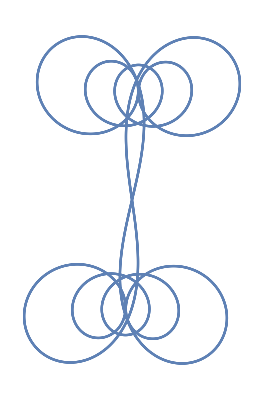
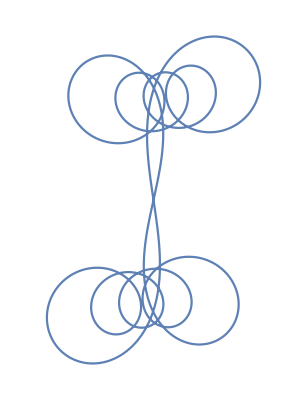
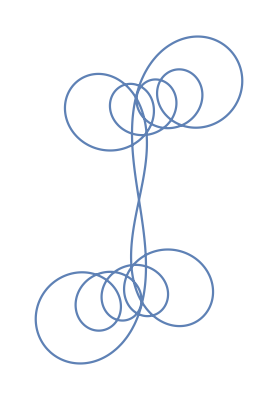
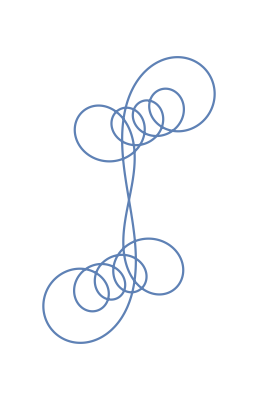
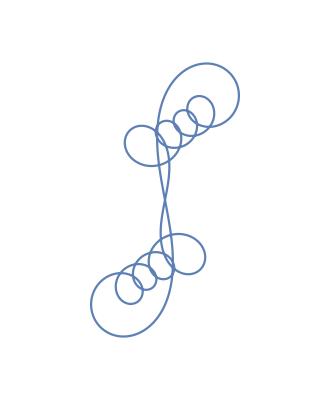
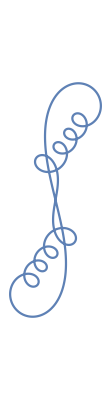
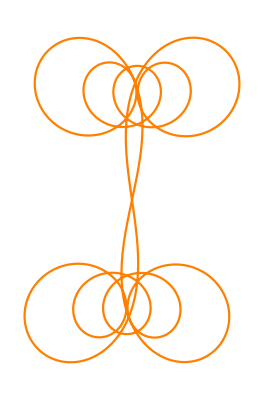
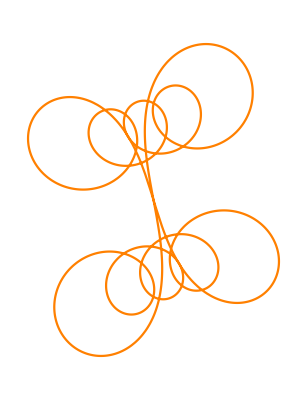
v = 0.05c | v = 0.23c | v = 0.41c | v = 0.59c | v = 0.77c | v = 0.95c
-Graphics-drift velocity = 0.0139663c | -Graphics-drift velocity = 0.0361724c | -Graphics-drift velocity = 0.067029c | -Graphics-drift velocity = 0.106202c | -Graphics-drift velocity = 0.164092c | -Graphics-drift velocity = 0.306259c
-Graphics-drift velocity = 0.0140471c | -Graphics-drift velocity = 0.0470638c | -Graphics-drift velocity = 0.109769c | -Graphics-drift velocity = 0.0840454c | -Graphics-drift velocity = 0.131069c | -Graphics-drift velocity = 0.470338c

```mathematica
relvsnonrel=
Grid[Transpose[
Table[Join[{Style["v = "<>ToString[v]<>"c",FontSize->14,FontWeight->Bold]},
comparisons[0.1,1.4,0.013,1,v,ImageSize->Tiny,Axes->None,ImagePadding->0.5]],
{v,0.05,0.95,0.9/5}]],
Spacings->{2,1},Alignment->{Center,Bottom}]
```

A gallery of 24 plots of the motion in the drift coordinates with random parameters.

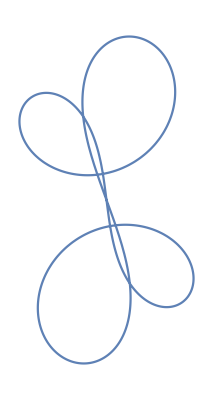
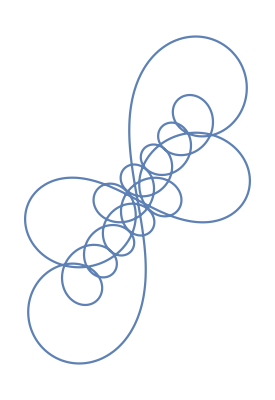
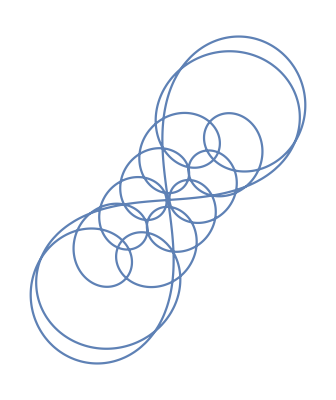
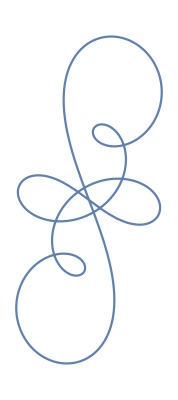
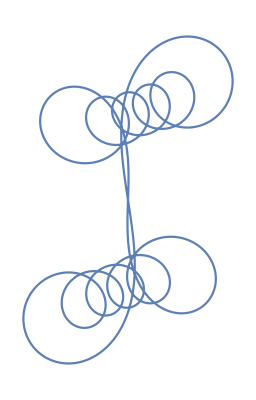
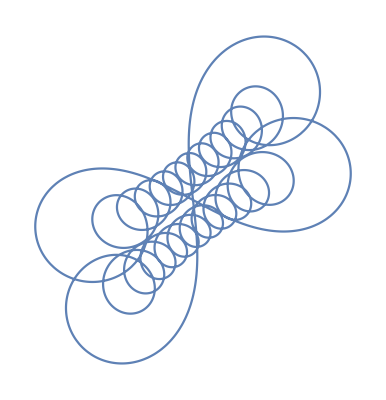
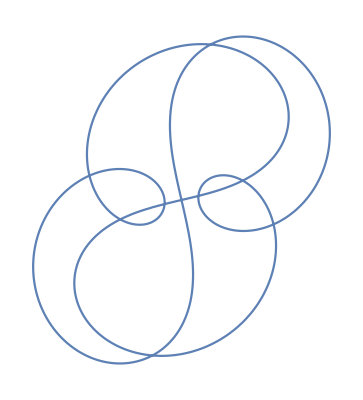
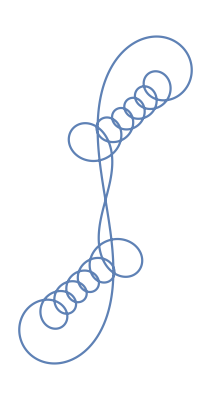
-Graphics-drift velocity = 0.181579c | -Graphics-drift velocity = 0.152166c | -Graphics-drift velocity = 0.0641517c | -Graphics-drift velocity = 0.436876c | -Graphics-drift velocity = 0.0649727c | -Graphics-drift velocity = 0.0377036c
-Graphics-drift velocity = 0.186965c | -Graphics-drift velocity = 0.167507c | -Graphics-drift velocity = 0.103526c | -Graphics-drift velocity = 0.0234634c | -Graphics-drift velocity = 0.121795c | -Graphics-drift velocity = 0.101772c
-Graphics-drift velocity = 0.0538857c | -Graphics-drift velocity = 0.26668c | -Graphics-drift velocity = 0.59225c | -Graphics-drift velocity = 0.395939c | -Graphics-drift velocity = 0.052219c | -Graphics-drift velocity = 0.504309c
-Graphics-drift velocity = 0.0266244c | -Graphics-drift velocity = 0.061919c | -Graphics-drift velocity = 0.0332189c | -Graphics-drift velocity = 0.0575102c | -Graphics-drift velocity = 0.118483c | -Graphics-drift velocity = 0.139704c

```mathematica
Grid[
Table[
Quiet@periodicplot[0.1,1.4,RandomReal[{-0.015,0.015}],RandomReal[{0.1,3}],RandomReal[{0.2,0.99}],planewavemotion,ImageSize->Tiny,Axes->False],
{4},{6}],
Spacings->{2,1},Alignment->{Center,Bottom}]
```

A manipulable plot of the drift coordinate motion of a relativistic particle.

```mathematica
Manipulate[
Tmax=30;
Quiet[periodicplot[1,qv,E0v,BE E0v,v0z+0.001,planewavemotion]],
{{E0v,2.3,"electric field strength"},0.1,3,0.1,Appearance->"Labeled"},
{{v0z,0.06,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{BE,1.6,"E/B ratio"},0.1,7,0.1,Appearance->"Labeled"},
{{qv,8.18,"charge to mass ratio"},-2,20,0.02,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

### Relativistic and Non-relativistic Dynamics in Circularly Polarized Waves

In circularly polarized waves, the E and B fields rotate with constant magnitude as the wave propagates perpendicular to the plane of rotation at the speed of light. The two fields remain perpendicular, though in the below animation only one of the two is shown.

```mathematica
Import["C:\Users\jackm\OneDrive\Documents\UNC Math 528L\circularpolarizationgif.gif","Animation",ControlPlacement->Top,AnimationRunning->False]
```

https://commons.wikimedia.org/wiki/File:Circular.Polarization.Circularly.Polarized.Light_Left.Hand.Animation.305x190.255Colors.gif

Nonrelativistic equations of motion for a particle in a circularly polarized wave propagating in the ẑ direction.

```mathematica
nonrelcircpolarizedmotion=Module[
{c=1,E,B,
r={x[t],y[t],z[t]},
v={x'[t],y'[t],z'[t]},
k={0,0,1}},
p=m0 v;
E= {E0 Cos[k.r-c t],E0 Sin[k.r-c t],0};
B= B0 Cross[k,E];
First@Solve[D[p,t]==q(E+Cross[v,B]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[nonrelcircpolarizedmotion]
```

x''[t]==(E0 q Cos[t-z[t]] (1-B0 z'[t]))/m0
y''[t]==(E0 q Sin[t-z[t]] (-1+B0 z'[t]))/m0
z''[t]==(B0 E0 q (Cos[t-z[t]] x'[t]-Sin[t-z[t]] y'[t]))/m0

Relativistic equations of motion for a particle in a circularly polarized wave propagating in the ẑ direction.

```mathematica
circpolarizedmotion=Module[
{c=1,E,B,
r={x[t],y[t],z[t]},
γ=(1-(x'[t]^2+y'[t]^2+z'[t]^2)/c^2)^(-1/2),
v={x'[t],y'[t],z'[t]},
k={0,0,1}},
γ=(1-v.v/c^2)^(-1/2);
p=γ m0 v;
E= {E0 Cos[k.r-c t],E0 Sin[k.r-c t],0};
B= B0 Cross[k,E];
First@Solve[D[p,t]==q(E+Cross[v,B]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[circpolarizedmotion]
```

x''[t]==-(E0 q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (Cos[t-z[t]] x'[t]^2-Sin[t-z[t]] x'[t] y'[t]+Cos[t-z[t]] (-1+B0 z'[t])))/m0
y''[t]==-(E0 q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (Cos[t-z[t]] x'[t] y'[t]-Sin[t-z[t]] (-1+y'[t]^2+B0 z'[t])))/m0
z''[t]==-(E0 q (Cos[t-z[t]] x'[t]-Sin[t-z[t]] y'[t]) (-B0+z'[t]) √(1-x'[t]^2-y'[t]^2-z'[t]^2))/m0

Manipulable plot of the trajectory of a nonrelativistic charged particle in a circularly polarized wave. The motion resembles two helical paths added together, one representing each of the E and B field forces on the particle.

```mathematica
Manipulate[
Tmax=100;

mvmtc=
NDSolveValue[Join[circpolarizedmotion/.{m0->1,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==v0z,z'[0]==0}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

Show[ParametricPlot3D[Through@mvmtc[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}],
Graphics3D[{Orange,PointSize-> .05,Point[{0,0,0}]}]],

{{E0v,0.044,"electric field strength"},0.,0.1,0.001,Appearance->"Labeled"},
{{B0v,1.3,"magnetic field strength"},0.05,2.,0.05,Appearance->"Labeled"},
{{v0z,0.12,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{qv,18.5,"charge/mass ratio of particle"},0,50,0.5,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

Manipulable comparison plots of the trajectory of relativistic and nonrelativistic charged particles in a circularly polarized wave.

```mathematica
Manipulate[
Tmax=50;

mvmtc=
NDSolveValue[Join[circpolarizedmotion/.{m0->1,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==v0z,z'[0]==0}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

mvmtnrc=
NDSolveValue[Join[nonrelcircpolarizedmotion/.{m0->1,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==v0z,z'[0]==0}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

Grid[{{"Non-Relativistic","Relativistic"},
{ParametricPlot3D[Through@mvmtnrc[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,400}],
ParametricPlot3D[Through@mvmtc[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,400}]}}],

{{E0v,0.12,"electric field strength"},0.,1.,0.001,Appearance->"Labeled"},
{{B0v,1.4,"magnetic field strength"},0.05,2.,0.05,Appearance->"Labeled"},
{{v0z,0.11,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{qv,2.,"charge/mass ratio of particle"},0,200,0.5,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

### Dynamics in Crossed Waves

In this section, the dynamics of a particle in a field of two waves propagating in the ŷ and ẑ directions are considered. I was inspired by L. Krlín, M. Zápotocký & V. Svoboda (2004), who concluded that a full relativistic regime causes stochastization of the dynamics. A figure from their paper showing the motion of one particle given by their corrected Hamiltonian solution (bold line) is below (the thin lines are a drift approximation that does not give rise to such behavior).

```mathematica
Import["C:\\Users\\jackm\\OneDrive\\Documents\\UNC Math 528L\\chaotictwowaves.PNG"]
```

-Graphics-

Nonrelativistic equations of motion for a particle in two crossed transverse waves of equal magnitude travelling in the ŷ and ẑ directions.

```mathematica
nonreldoubleplanewavemotion=Module[
{c=1,E1,B1,E2,B2,
r={x[t],y[t],z[t]},
v={x'[t],y'[t],z'[t]},
k1={0,0,1},
k2={0,1,0}},
p=m0 v;
E1= {E0 Sin[k1.r-c t],0,0};
B1= {0,B0 Sin[k1.r-c t],0};
E2= {0,0,E0 Sin[k2.r-c t]};
B2= {B0 Sin[k2.r-c t],0,0};
First@Solve[D[p,t]==q(E1+E2+Cross[v,B1+B2]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[nonreldoubleplanewavemotion]
```

x''[t]==(q Sin[t-z[t]] (-E0+B0 z'[t]))/m0
(B0 q Sin[t-y[t]] z'[t])/m0+y''[t]==0
(q (B0 Sin[t-z[t]] x'[t]+Sin[t-y[t]] (E0-B0 y'[t])))/m0+z''[t]==0

Relativistic equations of motion for a particle in two crossed transverse waves of equal magnitude travelling in the ŷ and ẑ directions.

```mathematica
doubleplanewavemotion=Module[
{c=1,E1,B1,E2,B2,
r={x[t],y[t],z[t]},
γ=(1-(x'[t]^2+y'[t]^2+z'[t]^2)/c^2)^(-1/2),
v={x'[t],y'[t],z'[t]},
k1={0,0,1},
k2={0,1,0}},
γ=(1-v.v/c^2)^(-1/2);
p=γ m0 v;
E1= {E0 Sin[k1.r-c t],0,0};
B1= {0,B0 Sin[k1.r-c t],0};
E2= {0,0,E0 Sin[k2.r-c t]};
B2= {B0 Sin[k2.r-c t],0,0};
First@Solve[D[p,t]==q(E1+E2+Cross[v,B1+B2]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[doubleplanewavemotion]
```

x''[t]==(q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (E0 Sin[t-z[t]] x'[t]^2+E0 Sin[t-y[t]] x'[t] z'[t]+Sin[t-z[t]] (-E0+B0 z'[t])))/m0
y''[t]==(q (E0 Sin[t-z[t]] x'[t] y'[t]+Sin[t-y[t]] (-B0+E0 y'[t]) z'[t]) √(1-x'[t]^2-y'[t]^2-z'[t]^2))/m0
z''[t]==(q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (-Sin[t-z[t]] x'[t] (B0-E0 z'[t])+Sin[t-y[t]] (B0 y'[t]+E0 (-1+z'[t]^2))))/m0

Manipulable plots of both the nonrelativistic and relativistic models for particle motion in the crossed transverse wave scenario. Though the similarities are not as apparent as in the simpler models, I think qualitatively more similarities are observed at lower velocities.

```mathematica
Manipulate[
Tmax=30;
dmvmtnr=
NDSolveValue[Join[nonreldoubleplanewavemotion/.{m0->mv,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];
dmvmtr=
NDSolveValue[Join[doubleplanewavemotion/.{m0->mv,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

Grid[{{"Non-relativistic","Relativistic"},
{ParametricPlot3D[Through@dmvmtnr[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}],
ParametricPlot3D[Through@dmvmtr[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}]}}],

{{mv,0.1,"rest mass of particle"},0.05,0.15,0.01,Appearance->"Labeled"},
{{E0v,0.013,"electric field strength"},0.001,0.05,0.001,Appearance->"Labeled"},
{{B0v,1.,"magnetic field strength"},0.05,2.,0.05,Appearance->"Labeled"},
{{v0z,0.07,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{qv,1.4,"charge of particle"},-2,2,0.02,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

The two-plane-wave system is highly sensitive to changes in initial conditions, as seen in this plot on 0 ≤ t ≤ 18.

```mathematica
Tmax=18;
dmvmtrchaos=
Table[NDSolveValue[Join[doubleplanewavemotion/.{m0->0.1,q->1.4,E0->0.021,B0->0.9},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==0.8+i}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity],{i,{0,0.0001,0.001,0.01}}];

Show[
Graphics3D[{Orange,PointSize-> .05,Point[{0,0,0}],
PointSize->Large,Black,Table[Point[Through@dmvmtrchaos[[i]][Tmax]],{i,1,4}]}],
ParametricPlot3D[Evaluate[Table[Through@dmvmtrchaos[[i]][t],{i,1,4}]],{t,0,Tmax},
PlotRange->All,PlotPoints->400,PlotStyle->Table[Hue[0.9-i/10.,0.62,0.68],{i,1,4}],
PlotLegends->Table["v = "<>ToString[0.8+i]<>"c",{i,{0,0.0001,0.001,0.01}}]]]
```

-Graphics3D-

For completeness, I also considered the motion of a relativistic particle in two crossed circularly polarized plane waves, with otherwise the same constraints as the above.

```mathematica
doublecircwavemotion=Module[
{c=1,E1,B1,E2,B2,
r={x[t],y[t],z[t]},
γ=(1-(x'[t]^2+y'[t]^2+z'[t]^2)/c^2)^(-1/2),
v={x'[t],y'[t],z'[t]},
k1={0,0,1},
k2={0,1,0}},
γ=(1-v.v/c^2)^(-1/2);
p=γ m0 v;
E1= {E0 Cos[k1.r-c t],E0 Sin[k1.r-c t],0};
B1=  B0 Cross[k1,E1];
E2= {E0 Sin[k2.r-c t],0,E0 Cos[k2.r-c t]};
B2= B0 Cross[k2,E2];
First@Solve[D[p,t]==q(E1+E2+Cross[v,B1+B2]),{x''[t],y''[t],z''[t]}]/.Rule->Equal//Simplify
];
Column[doublecircwavemotion]
```

x''[t]==-1/m0 E0 q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (-Cos[t-z[t]]+Sin[t-y[t]]+(Cos[t-z[t]]-Sin[t-y[t]]) x'[t]^2-B0 Sin[t-y[t]] y'[t]+B0 Cos[t-z[t]] z'[t]+x'[t] (-Sin[t-z[t]] y'[t]+Cos[t-y[t]] z'[t]))
y''[t]==1/m0 E0 q (-Sin[t-z[t]]+Sin[t-z[t]] y'[t]^2+x'[t] (-B0 Sin[t-y[t]]+(-Cos[t-z[t]]+Sin[t-y[t]]) y'[t])+B0 Cos[t-y[t]] z'[t]+B0 Sin[t-z[t]] z'[t]-Cos[t-y[t]] y'[t] z'[t]) √(1-x'[t]^2-y'[t]^2-z'[t]^2)
z''[t]==-1/m0 E0 q √(1-x'[t]^2-y'[t]^2-z'[t]^2) (-x'[t] (B0 Cos[t-z[t]]+(-Cos[t-z[t]]+Sin[t-y[t]]) z'[t])+y'[t] (B0 (Cos[t-y[t]]+Sin[t-z[t]])-Sin[t-z[t]] z'[t])+Cos[t-y[t]] (-1+z'[t]^2))

```mathematica
Manipulate[
Tmax=100;
dmvmtcr=
NDSolveValue[Join[doublecircwavemotion/.{m0->1,q->qv,E0->E0v,B0->B0v},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==v0z}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity];

ParametricPlot3D[Through@dmvmtcr[t],{t,0,Tmax},
PlotRange->All,PlotPoints->40*Tmax,ImageSize->{300,300}],

{{E0v,0.431,"electric field strength"},0.001,0.5,0.001,Appearance->"Labeled"},
{{B0v,0.8,"magnetic field strength"},0.05,2.,0.05,Appearance->"Labeled"},
{{v0z,0.07,"initial v/c"},0.01,0.99,0.01,Appearance->"Labeled"},
{{qv,14,"charge/mass ratio particle"},0,30,0.02,Appearance->"Labeled"},
ContinuousAction-> False,ControlPlacement->Top]
```

The system of crossed circularly polarized waves is sensitive to initial conditions on a longer time scale, though qualitatively it is not as “chaotic” as the crossed transverse wave scenario.

```mathematica
Tmax=60;
dmvmtcrchaos=
Table[NDSolveValue[Join[doublecircwavemotion/.{m0->0.1,q->1.42,E0->1.,B0->1.},
{x[0]==0,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==0.8+i}],
{x,y,z},{t,0,Tmax},MaxSteps->Infinity],{i,{0,0.0001,0.001,0.01}}];

Show[
Graphics3D[{Orange,PointSize-> .05,Point[{0,0,0}],
PointSize->Large,Black,Table[Point[Through@dmvmtcrchaos[[i]][Tmax]],{i,1,4}]}],
ParametricPlot3D[Evaluate[Table[Through@dmvmtcrchaos[[i]][t],{i,1,4}]],{t,0,Tmax},
PlotRange->All,PlotPoints->400,PlotStyle->Table[Hue[0.9-i/10.,0.62,0.68],{i,1,4}],
PlotLegends->Table["v = "<>ToString[0.8+i]<>"c",{i,{0,0.0001,0.001,0.01}}]]]
```

-Graphics3D-